```mathematica
A=197; (*Pb*)
r0=6.38;(*fm*)
a=0.535 ;(*fm*)
σ=4.2;(*mb/10=fm^2, at √s=200GeV*)
ws[s_,z_]:=1/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1[s1_,s2_,ang_,z_]:=1/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
ρ0=1/NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}];
wsn[s_,z_]:=ρ0/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1n[s1_,s2_,ang_,z_]:=ρ0/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
T[s_]:=NIntegrate[wsn[s,z],{z,-∞,∞}]
T1[s1_,s2_,ang_]:=NIntegrate[ws1n[s1,s2,ang,z],{z,-∞,∞}]
TAA[b_]:=Quiet[NIntegrate[s T1[s,b,ang]T[s],{s,0,∞},{ang,0,2 π}]]
```

```mathematica
TAA[0]
```

0.00755886

```mathematica
T[0]
```

0.0109688

```mathematica
TAAtab=ParallelTable[{x,TAA[x]},{x,0,14,0.5}]
```

{{0.,0.00755886},{0.5,0.00751234},{1.,0.00737579},{1.5,0.00715744},{2.,0.00686881},{2.5,0.00652269},{3.,0.00613166},{3.5,0.00570736},{4.,0.00526028},{4.5,0.00479973},{5.,0.00433401},{5.5,0.00387051},{6.,0.00341587},{6.5,0.00297601},{7.,0.00255622},{7.5,0.00216116},{8.,0.00179489},{8.5,0.00146081},{9.,0.00116165},{9.5,0.000899401},{10.,0.000675182},{10.5,0.000489125},{11.,0.000340195},{11.5,0.000226026},{12.,0.000142858},{12.5,0.0000856988},{13.,0.0000488142},{13.5,0.0000264886},{14.,0.0000137697}}

```mathematica
TAAtab={{0.,0.007558864026676659},{0.5,0.007512344944835761},{1.,0.007375794206194003},{1.5,0.007157443030325738},{2.,0.006868813321135529},{2.5,0.006522687805327265},{3.,0.006131655042115531},{3.5,0.005707362588169074},{4.,0.005260280790053637},{4.5,0.004799730255244412},{5.,0.004334005125451636},{5.5,0.003870508969510548},{6.,0.003415867424987254},{6.5,0.0029760095747562586},{7.,0.0025562199284275447},{7.5,0.0021611637271957414},{8.,0.0017948888038114349},{8.5,0.0014608073847004327},{9.,0.0011616513707443988},{9.5,0.0008994009779430287},{10.,0.0006751822609073516},{10.5,0.0004891254220643536},{11.,0.00034019471318897623},{11.5,0.00022602561531308052},{12.,0.00014285813914476864},{12.5,0.00008569877804828624},{13.,0.00004881420258704518},{13.5,0.000026488575621041624},{14.,0.00001376971539148656}};
```

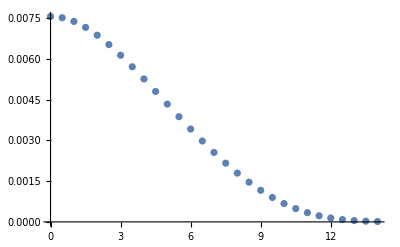

```mathematica
ListPlot[TAAtab]
```

```mathematica
TAAinter=Interpolation[TAAtab];
```

```mathematica
NIntegrate[2π x TAAinter[x],{x,0,14}]
```

0.999115

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

0.999999

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-σ T[s])^A),{s,0,∞},{ang,0,2 π}]];
```

```mathematica
Ncoll[b_]:=A^2 σ TAA[b];
```

```mathematica
Ncoll[0]
```

1232.08

```mathematica
NpartTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NpartTab];
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
NcollTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NcollTab]
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
ParallelDo[NpartTab[[i,2]]=Npart[NpartTab[[i,1]]],{i,Length[NpartTab]}]//AbsoluteTiming
```

{1490.09,Null}

```mathematica
ParallelDo[NcollTab[[i,2]]=Ncoll[NcollTab[[i,1]]],{i,Length[NcollTab]}]//AbsoluteTiming
```

{1391.95,Null}

```mathematica
NpartTab
```

{{0.,378.802},{0.1,378.743},{0.2,378.565},{0.3,378.269},{0.4,377.854},{0.5,377.32},{0.6,376.668},{0.7,375.895},{0.8,375.006},{0.9,373.998},{1.,372.871},{1.1,371.627},{1.2,370.266},{1.3,368.789},{1.4,367.196},{1.5,365.49},{1.6,363.672},{1.7,361.743},{1.8,359.706},{1.9,357.562},{2.,355.314},{2.5,342.611},{3.,327.734},{3.5,311.073},{4.,293.004},{4.5,273.878},{5.,254.008},{5.5,233.672},{6.,213.124},{6.5,192.593},{7.,172.291},{7.5,152.415},{8.,133.152},{8.5,114.678},{9.,97.1626},{9.5,80.7684},{10.,65.6516},{10.5,51.9618},{11.,39.8388},{11.5,29.4057},{12.,20.7526},{12.1,19.2397},{12.2,17.7993},{12.3,16.4311},{12.4,15.1346},{12.5,13.9091},{12.6,12.7537},{12.7,11.6672},{12.8,10.6485},{12.9,9.69581},{13.,8.80756},{13.1,7.98179},{13.2,7.21638},{13.3,6.50904},{13.4,5.85734},{13.5,5.25874},{13.6,4.71056},{13.7,4.21007},{13.8,3.75449},{13.9,3.341},{14.,2.96681},{14.1,2.62914},{14.2,2.32528},{14.3,2.05258},{14.4,1.80849},{14.5,1.59056},{14.6,1.39647},{14.7,1.22401},{14.8,1.07114},{14.9,0.935913},{15.,0.816553}}

```mathematica
NpartTab={{0.,378.80202013894785},{0.1,378.74275037928555},{0.2,378.5649960720415},{0.30000000000000004,378.2686674707589},{0.4,377.85367676414194},{0.5,377.31997907423755},{0.6000000000000001,376.6675215081528},{0.7000000000000001,375.89484424706717},{0.8,375.00641220844653},{0.9,373.9980254968526},{1.,372.87146851866305},{1.1,371.6272257471181},{1.2000000000000002,370.2659679304428},{1.3,368.7885706940277},{1.4000000000000001,367.19614083671155},{1.5,365.48997853463453},{1.6,363.67158786520156},{1.7000000000000002,361.74279123219117},{1.8,359.70553177410284},{1.9000000000000001,357.56198390206094},{2.,355.3144958695577},{2.5,342.61093602026347},{3.,327.73432102020575},{3.5,311.072608104606},{4.,293.00446209464786},{4.5,273.87843714721964},{5.,254.00758757005136},{5.5,233.67196332357815},{6.,213.12379695983495},{6.5,192.5927564338881},{7.,172.29064320020822},{7.5,152.41484688972653},{8.,133.15165601286435},{8.5,114.67785756309947},{9.,97.16259819099758},{9.5,80.76840574308231},{10.,65.6516213482929},{10.5,51.96178319495709},{11.,39.83881745149888},{11.5,29.405698605817204},{12.,20.752621870686372},{12.1,19.2396833429672},{12.2,17.799281233019943},{12.299999999999999,16.43108667404205},{12.4,15.134587943399504},{12.5,13.909082256594612},{12.6,12.753665998235322},{12.7,11.667229078807425},{12.799999999999999,10.648452423715687},{12.9,9.695808064427082},{13.,8.807563740248126},{13.1,7.981790629086733},{13.2,7.216375757506756},{13.3,6.509036951982307},{13.4,5.857343790000809},{13.5,5.258737989817142},{13.6,4.710559055637524},{13.7,4.2100704567365765},{13.8,3.754486503550584},{13.9,3.3410003736514646},{14.,2.966809500191921},{14.1,2.6291419146723105},{14.2,2.3252788846718038},{14.3,2.052576041698857},{14.4,1.8084935745609756},{14.5,1.590561890082674},{14.6,1.3964678198442182},{14.7,1.2240140075969694},{14.8,1.0711374270733847},{14.9,0.935912645979184},{15.,0.8165528008662291}};
```

```mathematica
NcollTab
```

{{0.,1232.08},{0.1,1231.77},{0.2,1230.86},{0.3,1229.34},{0.4,1227.22},{0.5,1224.5},{0.6,1221.19},{0.7,1217.29},{0.8,1212.83},{0.9,1207.81},{1.,1202.24},{1.1,1196.13},{1.2,1189.5},{1.3,1182.37},{1.4,1174.75},{1.5,1166.65},{1.6,1158.09},{1.7,1149.09},{1.8,1139.66},{1.9,1129.83},{2.,1119.6},{2.5,1063.18},{3.,999.446},{3.5,930.288},{4.,857.414},{4.5,782.345},{5.,706.433},{5.5,630.884},{6.,556.779},{6.5,485.083},{7.,416.658},{7.5,352.265},{8.,292.563},{8.5,238.108},{9.,189.347},{9.5,146.6},{10.,110.053},{10.5,79.7264},{11.,55.451},{11.5,36.8417},{12.,23.2856},{12.1,21.1119},{12.2,19.1009},{12.3,17.2452},{12.4,15.537},{12.5,13.9687},{12.6,12.5326},{12.7,11.221},{12.8,10.0261},{12.9,8.94049},{13.,7.95661},{13.1,7.06723},{13.2,6.2653},{13.3,5.54401},{13.4,4.89685},{13.5,4.31758},{13.6,3.80029},{13.7,3.3394},{13.8,2.92966},{13.9,2.56619},{14.,2.24443},{14.1,1.96017},{14.2,1.70951},{14.3,1.48891},{14.4,1.29509},{14.5,1.12511},{14.6,0.976288},{14.7,0.846178},{14.8,0.732606},{14.9,0.633614},{15.,0.547449}}

```mathematica
Ncolltab={{0.,1232.0782068474368},{0.1,1231.7727293662679},{0.2,1230.859248630568},{0.30000000000000004,1229.3386569542204},{0.4,1227.2155649277813},{0.5,1224.4956988493504},{0.6000000000000001,1221.185953020914},{0.7000000000000001,1217.294603586564},{0.8,1212.832115207291},{0.9,1207.8092678349913},{1.,1202.238228862369},{1.1,1196.1321187254832},{1.2000000000000002,1189.5049484646072},{1.3,1182.3714562196678},{1.4000000000000001,1174.7470086231804},{1.5,1166.6474675684287},{1.6,1158.0891393984596},{1.7000000000000002,1149.088244453213},{1.8,1139.662457418436},{1.9000000000000001,1129.8277607758616},{2.,1119.601459955785},{2.5,1063.1837623551726},{3.,999.4462822237391},{3.5,930.2875456738652},{4.,857.4141961610048},{4.5,782.3454721982777},{5.,706.4333006373408},{5.5,630.8844469104865},{6.,556.7788753645875},{6.5,485.08301346420575},{7.,416.6582246498473},{7.5,352.26493297270605},{8.,292.56292626589556},{8.5,238.10838992992421},{9.,189.34661779832138},{9.5,146.60038072256222},{10.,110.05322312692432},{10.5,79.7263677205611},{11.,55.45098982143411},{11.5,36.84167803967844},{12.,23.285562392691173},{12.1,21.11191641400607},{12.2,19.10094228671289},{12.299999999999999,17.24516597367502},{12.4,15.536984960002032},{12.5,13.968712284558952},{12.6,12.532619589983497},{12.7,11.22098489486877},{12.799999999999999,10.026133803137336},{12.9,8.940488584932988},{13.,7.956607630442673},{13.1,7.067227005158699},{13.2,6.265296729113328},{13.3,5.544014114306378},{13.4,4.8968511388349585},{13.5,4.317579551363419},{13.6,3.8002880587053993},{13.7,3.339396333171773},{13.8,2.929664006867539},{13.9,2.5661941773571413},{14.,2.244433315438448},{14.1,1.9601669103319692},{14.2,1.7095118500762858},{14.3,1.4889056001144176},{14.4,1.2950935511342154},{14.5,1.1251139376664634},{14.6,0.9762880146890299},{14.7,0.8461778932752313},{14.8,0.7326064041851661},{14.9,0.6336143477405426},{15.,0.5474491077535242}};
```

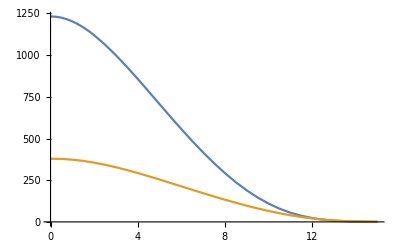

```mathematica
ListPlot[{NcollTab,NpartTab},Joined->True]
```